```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
InitializationValue[$Initialization] = Hold[$HistoryLength = 2];
<<"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\Kay-initialization.m"
"Directory for read/write is \"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\MathematicaFiles-LRW-DLA-bLRW\\LaplaceEqSolver&MORE\\\""
```

Directory for read/write is "D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA-bLRW\LaplaceEqSolver&MORE\"

Directory for read/write is "D:\Offline_Documents\University\PhD_Paris\PhD_work\Simulations\MathematicaFiles-LRW-DLA-bLRW\LaplaceEqSolver&MORE\"

## Import LRW data and plot it

convergenceData2026 - 01 - 16 - 13h47

```mathematica
dataConv=Drop[Import["..\\Data\\convergenceData2026-01-16-13h47.csv","CSV"],0];
```

```mathematica
dataConv[[1]]
```

{#i,Seed,R12,R15,R12R23,R12R25,R15R52,R15R52R23,R15R54,R12R23R34,R12R25R54,R15R52R23R34}

```mathematica
plots=Table["plot"<>ToString[dataConv[[1,i]]],{i,2,Length[dataConv[[1]]]}]
```

{plotSeed,plotR12,plotR15,plotR12R23,plotR12R25,plotR15R52,plotR15R52R23,plotR15R54,plotR12R23R34,plotR12R25R54,plotR15R52R23R34}

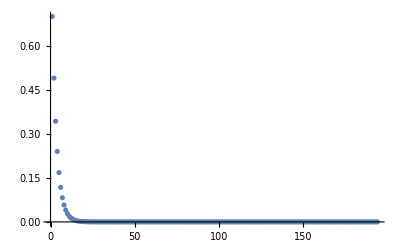
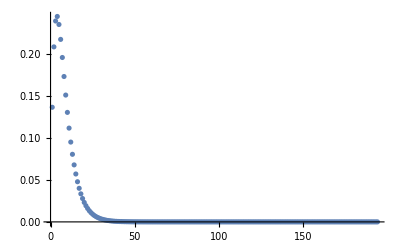
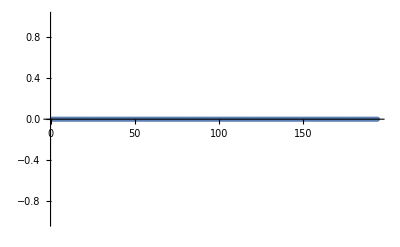
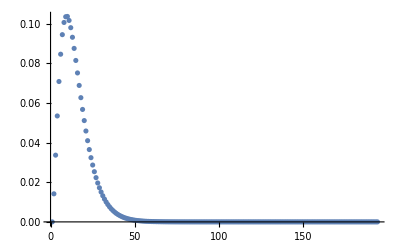
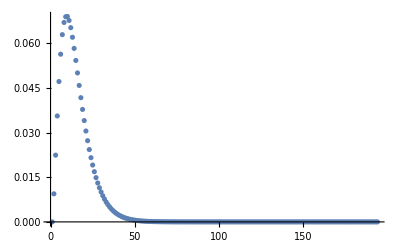
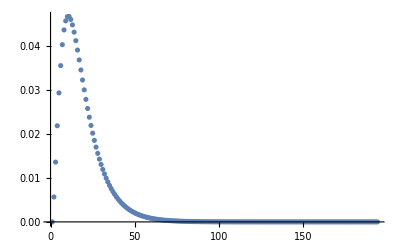
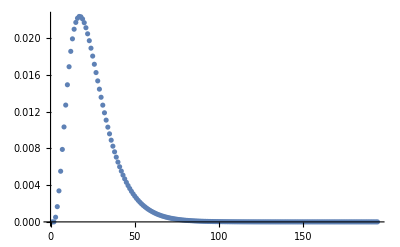
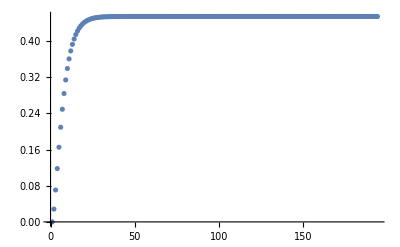

```mathematica
Table[plots[[i-1]]=ListPlot[dataConv[[2;;-1,{1,i}]],PlotRange->All],{i,2,Length[dataConv[[1]]]}]
```

```mathematica
plots=plots/. Point[x_]:>{PointSize[0.007],Point[x]};
plots[[1]]=plots[[1]]/. Point[x_]:>{PointSize[0.007],Red,Point[x]};
plots[[2]]=plots[[2]]/. Point[x_]:>{PointSize[0.007],Darker@Green,Point[x]};
plots[[3]]=plots[[3]]/. Point[x_]:>{PointSize[0.007],Darker@Green,Point[x]};
plots[[4]]=plots[[4]]/. Point[x_]:>{PointSize[0.007],Darker@Green,Point[x]};
plots[[5]]=plots[[5]]/. Point[x_]:>{PointSize[0.007],Darker@Green,Point[x]};
plots[[6]]=plots[[6]]/. Point[x_]:>{PointSize[0.007],Darker@Green,Point[x]};
plots[[7]]=plots[[7]]/. Point[x_]:>{PointSize[0.007],Darker@Green,Point[x]};
plots[[8]]=plots[[8]]/. Point[x_]:>{PointSize[0.007],Blue,Point[x]};
plots[[9]]=plots[[9]]/. Point[x_]:>{PointSize[0.007],Blue,Point[x]};
plots[[10]]=plots[[10]]/. Point[x_]:>{PointSize[0.007],Blue,Point[x]};
plots[[11]]=plots[[11]]/. Point[x_]:>{PointSize[0.007],Blue,Point[x]};
```

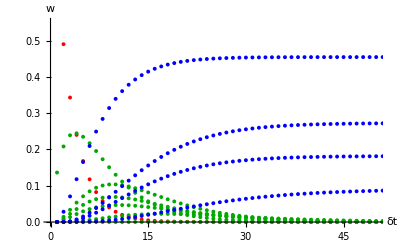

```mathematica
Show[plots,PlotRange->{{0,50},{0,0.55}},AxesLabel->{δt,w},AxesOrigin->{0,0}]
```

convergenceData2026-01-16-16h01

```mathematica
dataConv=Drop[Import["..\\Data\\convergenceData2026-01-16-16h01.csv","CSV"],0];
```

```mathematica
ClearAll[plots]
```

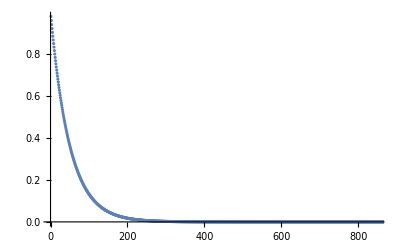
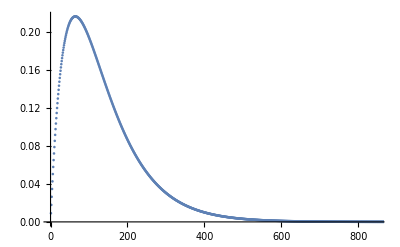
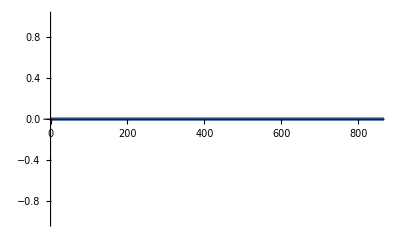
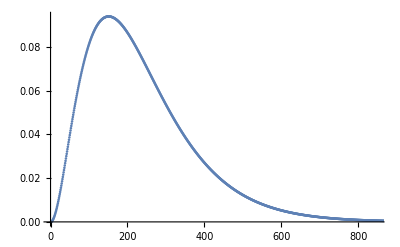
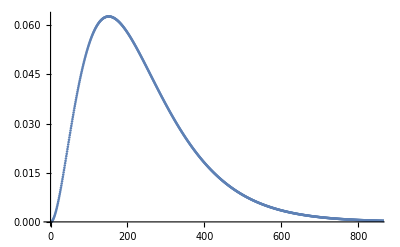
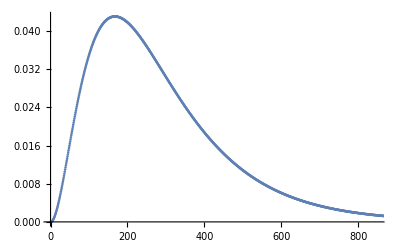
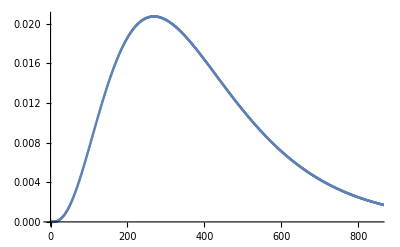
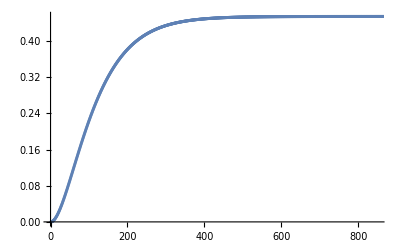

```mathematica
plots=Table[ListPlot[dataConv[[2;;-1,{1,i}]],PlotRange->{{0,xEndRange},All}],{i,2,Length[dataConv[[1]]]}]
```

```mathematica
size=0.0035;
plots=plots/. Point[x_]:>{PointSize[size],Point[x]};
plots[[1]]=plots[[1]]/. Point[x_]:>{PointSize[size],Red,Point[x]};
plots[[2]]=plots[[2]]/. Point[x_]:>{PointSize[size],Darker@Green,Point[x]};
plots[[3]]=plots[[3]]/. Point[x_]:>{PointSize[size],Darker@Green,Point[x]};
plots[[4]]=plots[[4]]/. Point[x_]:>{PointSize[size],Darker@Green,Point[x]};
plots[[5]]=plots[[5]]/. Point[x_]:>{PointSize[size],Darker@Green,Point[x]};
plots[[6]]=plots[[6]]/. Point[x_]:>{PointSize[size],Darker@Green,Point[x]};
plots[[7]]=plots[[7]]/. Point[x_]:>{PointSize[size],Darker@Green,Point[x]};
plots[[8]]=plots[[8]]/. Point[x_]:>{PointSize[size],Blue,Point[x]};
plots[[9]]=plots[[9]]/. Point[x_]:>{PointSize[size],Blue,Point[x]};
plots[[10]]=plots[[10]]/. Point[x_]:>{PointSize[size],Blue,Point[x]};
plots[[11]]=plots[[11]]/. Point[x_]:>{PointSize[size],Blue,Point[x]};
plotsRestricted=plots/.PlotRange->{{0,xEndRange},All};
```

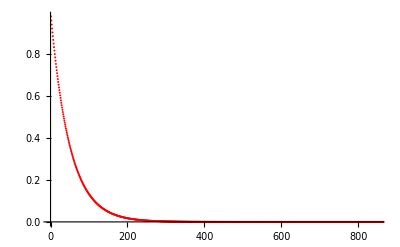
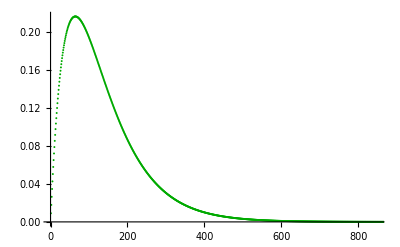
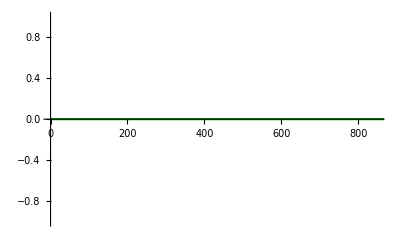
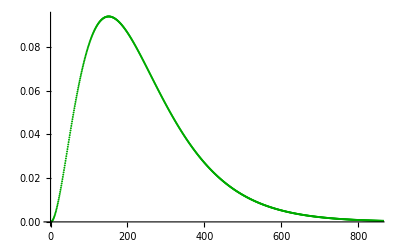
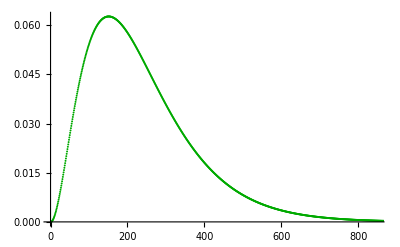
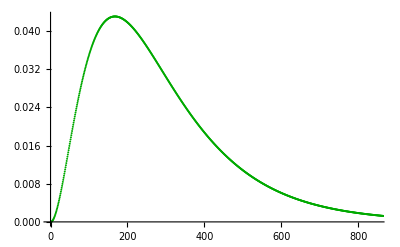
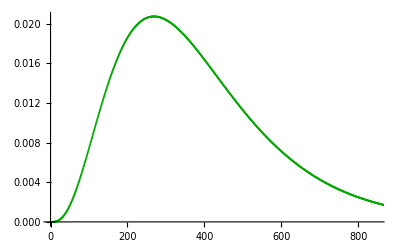
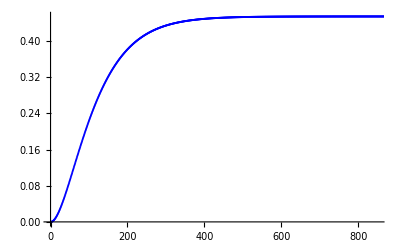

```mathematica
plots
```

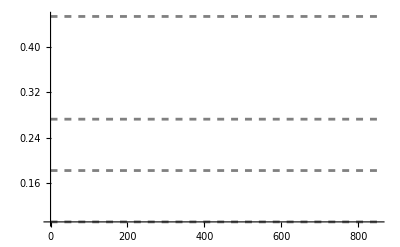

```mathematica
analyticalLines=Plot[{1/11,2/11,3/11,5/11},{x,0,850},
PlotStyle->Directive[Gray,Dashed],
(*PlotRange->All,PlotLegends->{"1/11","2/11","3/11","5/11"},*)
Epilog->{Text["1/11",{textx,1/11}]}]
```

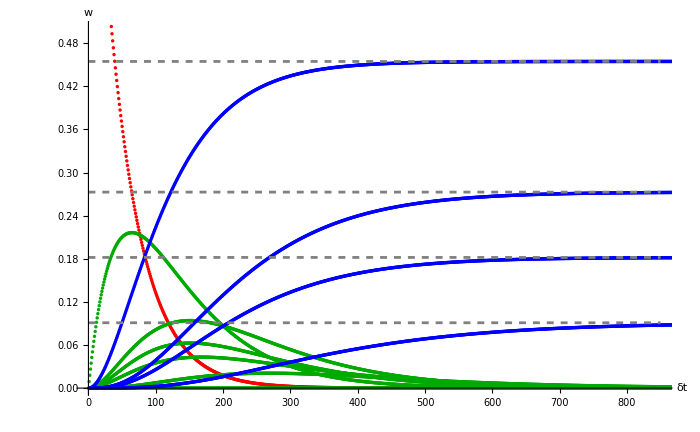

```mathematica
xEndRange=850;
textx=xEndRange+20;
Show[{plots,analyticalLines},
PlotRange->{{0,xEndRange},{0,5/10}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
AxesLabel->{δt,w},
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},
Background->None,
Epilog->{
Text["1/11",Offset[{0,0},{textx,1/11}]],Text["2/11",{textx,2/11}],Text["3/11",{textx,3/11}],Text["5/11",{textx,5/11}]}]
```

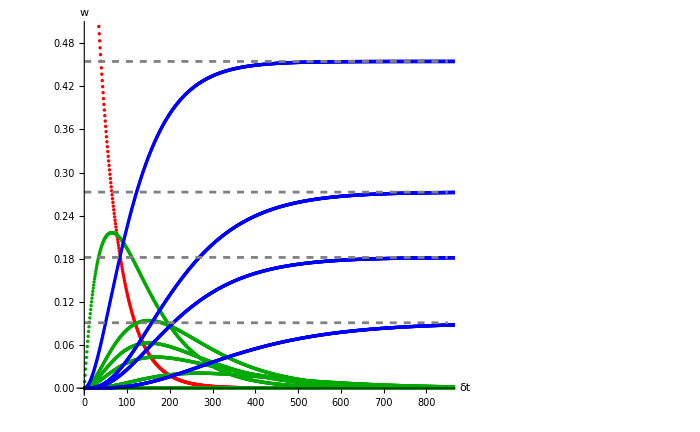

```mathematica
xEndRange=850;
textx=xEndRange+20;
Show[{Show[{plots,analyticalLines},
PlotRange->{{0,xEndRange},{0,5/10}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
AxesLabel->{δt,w},
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},
Background->None
(*Epilog->{
Text["1/11",{textx,1/11}],Text["2/11",{textx,2/11}],Text["3/11",{textx,3/11}],Text["5/11",{textx,5/11}]}*)],Graphics[{Text["1/11",Offset[{textx,0},{xEndRange,1/11}]]}]
}]
```

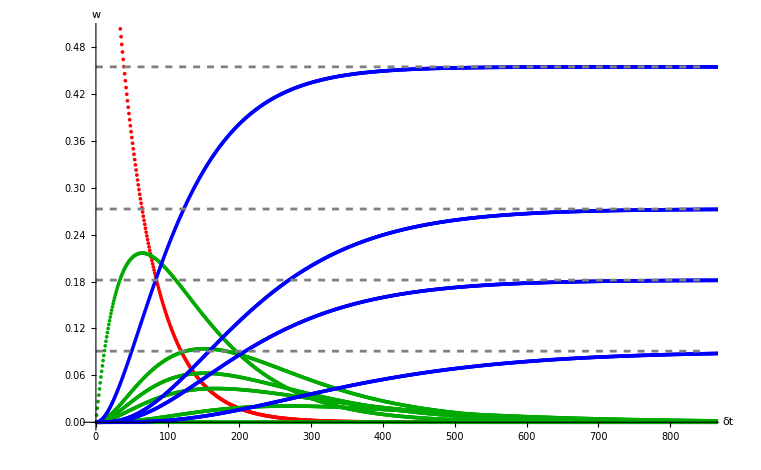

convergenceData2026-01-19-09h40

```mathematica
dataLRWConv=Drop[Import["..\\Data\\convergenceData2026-01-19-09h40.csv","CSV"],0];
```

```mathematica
ClearAll[plots]
```

```mathematica
dataLRWConv[[1]]
```

{#i,Seed,R12,R15,R12R23,R12R25,R15R52,R15R52R23,R15R54,R12R23R34,R12R25R54,R15R52R23R34}

```mathematica
plotsLRW=Table[
ListPlot[
Callout[Times[{gamma,1},#]&/@dataLRWConv[[2;;-1,{1,i}]],dataLRWConv[[1,i]],Above],
PlotRange->All(*, PlotLabel->dataConv[[1,i]]*)],{i,2,Length[dataLRWConv[[1]]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

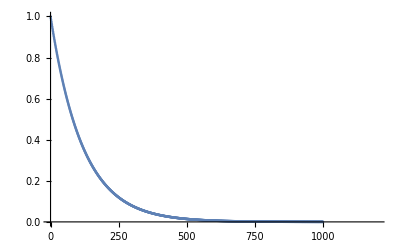
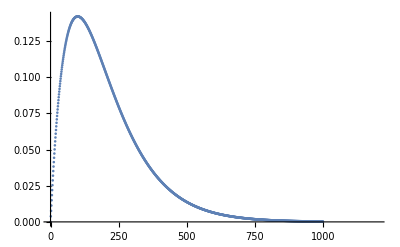
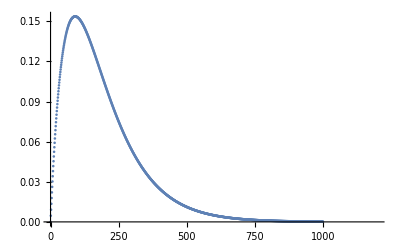
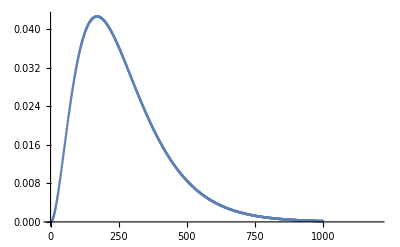
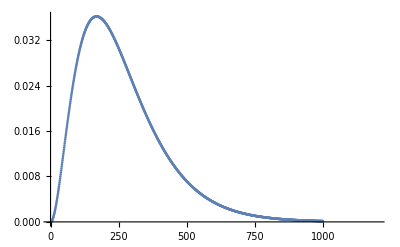
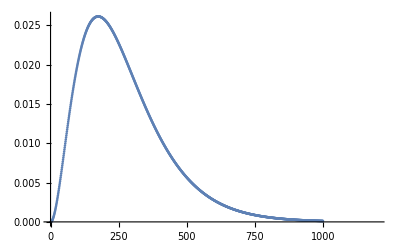
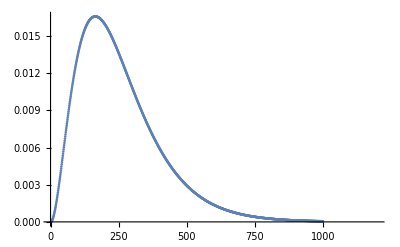
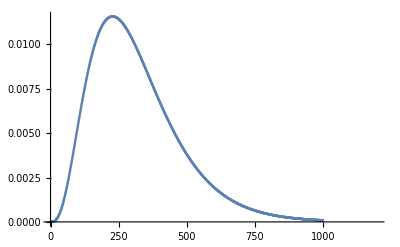

```mathematica
plotsLRW
```

```mathematica
size=0.0035;
plotsLRW=plotsLRW/. Point[x_]:>{PointSize[size],Point[x]};
plotsLRW[[1]]=plotsLRW[[1]]/. Point[x_]:>{PointSize[size],Red,Point[x]};
plotsLRW[[2]]=plotsLRW[[2]]/. Point[x_]:>{PointSize[size],RGBColor[0, Rational[2, 3], 0],Point[x]};
plotsLRW[[3]]=plotsLRW[[3]]/. Point[x_]:>{PointSize[size],RGBColor[0, 0.72, 0],Point[x]};
plotsLRW[[4]]=plotsLRW[[4]]/. Point[x_]:>{PointSize[size],RGBColor[0, 0.77, 0],Point[x]};
plotsLRW[[5]]=plotsLRW[[5]]/. Point[x_]:>{PointSize[size],RGBColor[0, 0.8200000000000001, 0],Point[x]};
plotsLRW[[6]]=plotsLRW[[6]]/. Point[x_]:>{PointSize[size],RGBColor[0, 0.87, 0],Point[x]};
plotsLRW[[7]]=plotsLRW[[7]]/. Point[x_]:>{PointSize[size],RGBColor[0, 0.92, 0],Point[x]};
plotsLRW[[8]]=plotsLRW[[8]]/. Point[x_]:>{PointSize[size],Blue,Point[x]};
plotsLRW[[9]]=plotsLRW[[9]]/. Point[x_]:>{PointSize[size],Blue,Point[x]};
plotsLRW[[10]]=plotsLRW[[10]]/. Point[x_]:>{PointSize[size],Blue,Point[x]};
plotsLRW[[11]]=plotsLRW[[11]]/. Point[x_]:>{PointSize[size],Blue,Point[x]};
plotsLRWRestricted=plotsLRW/.PlotRange->{{0,xEndRange},All};
```

```mathematica
plotsLRW
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
analyticalLines=Plot[{1/11,2/11,3/11,5/11},{x,0,850},
PlotStyle->Directive[Gray,Dashed],
(*PlotRange->All,PlotLegends->{"1/11","2/11","3/11","5/11"},*)
Epilog->{Text["1/11",{textx,1/11}]}]
```

-Graphics-

First plot

```mathematica
xEndRange=1200;
textx=xEndRange+20;
Show[{plotsLRW,analyticalLines},
PlotRange->{{0,xEndRange},{0,5/10}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
AxesLabel->{δt,w},
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,20},{Automatic,Automatic}},
Background->None,
Epilog->{
Text["1/11",Offset[{0,0},{textx,1/11}]],Text["2/11",{textx,2/11}],Text["3/11",{textx,3/11}],Text["5/11",{textx,5/11}]}]
```

-Graphics-

Second plot

```mathematica
Times[{1,5},#]&/@{{2,3},{1,4},{1,4},{1,4},{1,4},{1,4}}
```

{{2,15},{1,20},{1,20},{1,20},{1,20},{1,20}}

```mathematica
gamma=0.01;

plotsLRWLine=Table[
ListLinePlot[
Prepend[Times[{gamma,1},#]&/@dataConv[[2;;-1,{1,i}]],If[i==2,{0,1},{0,0}]],
PlotRange->All, 
PlotLabel->dataConv[[1,i]]
],
{i,2,Length[dataConv[[1]]]}];
```

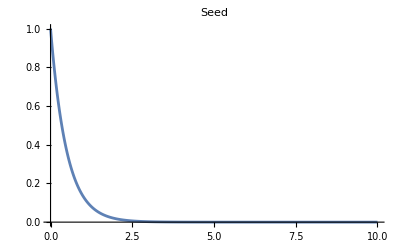
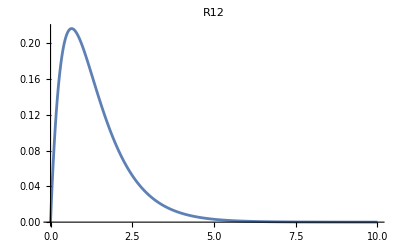
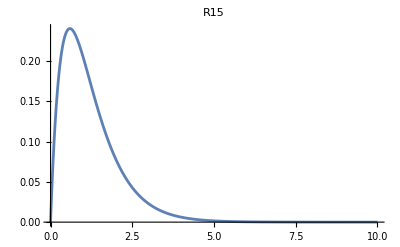
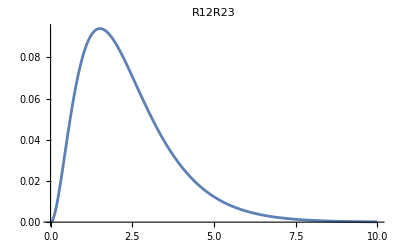
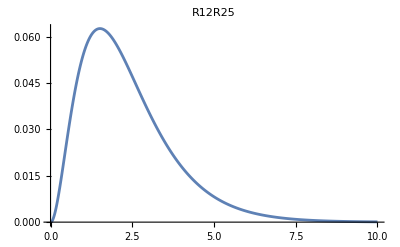
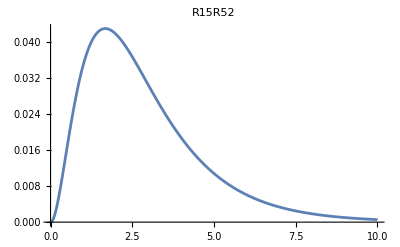
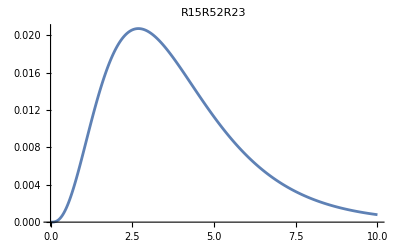
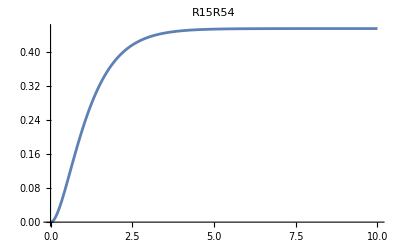

```mathematica
plotsLRWLine
```

```mathematica
(1-0.57)/5+0.57
```

0.656

```mathematica
size=0.0035;
plotsLRWLine=plotsLRWLine/. Line[x_]:>{Thickness[size],Line[x]};
plotsLRWLine[[1]]=plotsLRWLine[[1]]/. Line[x_]:>{Thickness[size],Red,Line[x]};
plotsLRWLine[[3]]=plotsLRWLine[[3]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLRWLine[[2]]=plotsLRWLine[[2]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.6, 0],Line[x]};
plotsLRWLine[[4]]=plotsLRWLine[[4]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.7000000000000001, 0],Line[x]};
plotsLRWLine[[5]]=plotsLRWLine[[5]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.8, 0],Line[x]};
plotsLRWLine[[6]]=plotsLRWLine[[6]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.9, 0],Line[x]};
plotsLRWLine[[7]]=plotsLRWLine[[7]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLRWLine[[8]]=plotsLRWLine[[8]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLRWLine[[9]]=plotsLRWLine[[9]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLRWLine[[10]]=plotsLRWLine[[10]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLRWLine[[11]]=plotsLRWLine[[11]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLRWLineRestricted=plotsLRWLine/.PlotRange->{{0,xEndRange},All};
```

```mathematica
analyticalLines=Plot[{1/11,2/11,3/11,5/11},{x,0,850*gamma},
PlotStyle->Directive[Gray,Dashed],
(*PlotRange->All,PlotLegends->{"1/11","2/11","3/11","5/11"},*)
Epilog->{Text["1/11",{textx,1/11}]}];
```

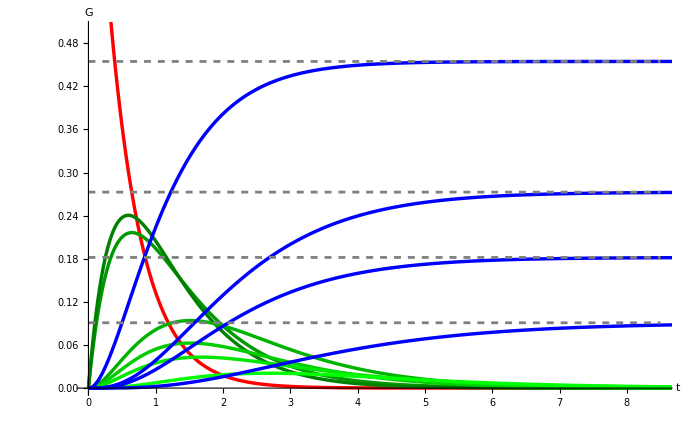

```mathematica
xEndRange=850*gamma;
textx=xEndRange+20;
Show[{plotsLRWLine,analyticalLines},
PlotLabel->None,
PlotRange->{{0,xEndRange},{0,5/10}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
AxesLabel->{t,G},
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,20},{Automatic,Automatic}},
Background->None
(*,Epilog->{
Text["1/11",Offset[{0,0},{textx,1/11}]],Text["2/11",{textx,2/11}],Text["3/11",{textx,3/11}],Text["5/11",{textx,5/11}]}*)]
```

## Import DLA data and plot it

DLAconvergenceData2026-01-22-23h54

```mathematica
dataConv=Drop[Import["..\\Data\\DLAconvergenceData2026-01-22-23h54.csv","CSV"],0];
```

```mathematica
ClearAll[plots]
```

```mathematica
dataConv[[1]]
```

{#i,Seed,R12,R15,R12R15,R12R23,R12R25,R15R52,R12R25R23,R15R52R23,R12R15R54,R15R52R54,R12R15R23R34,R12R15R23R54,R12R25R23R34,R12R25R23R54,R15R52R23R54,R15R54,R12R23R34,R12R25R54,R15R52R23R34}

```mathematica
plotsLine=Table[ListLinePlot[dataConv[[2;;-1,{1,i}]],PlotRange->All, PlotLabel->dataConv[[1,i]]],{i,2,Length[dataConv[[1]]]}];
```

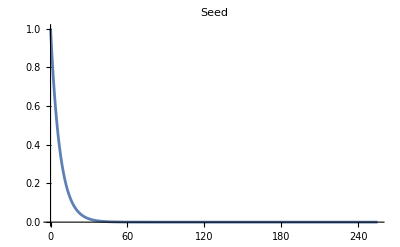
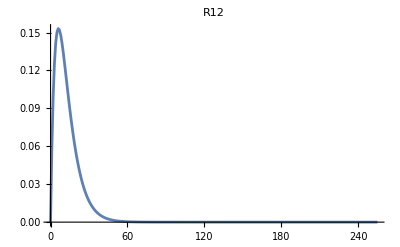
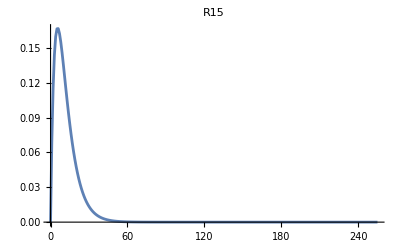
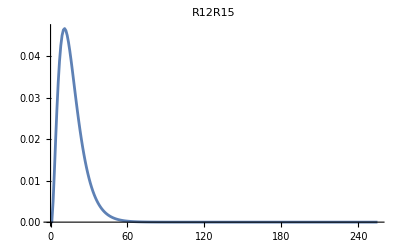
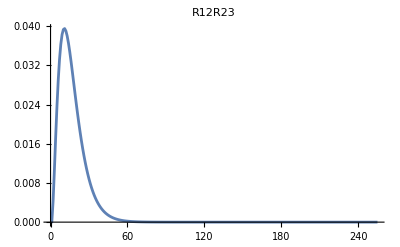
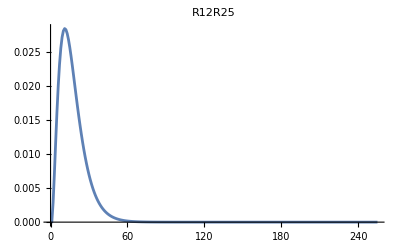
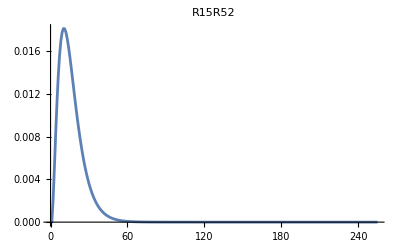
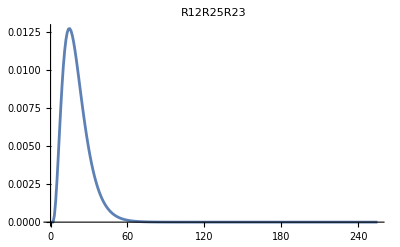

```mathematica
plotsLine
```

```mathematica
size=0.0035;
plotsLine=plotsLine/. Line[x_]:>{Thickness[size],Line[x]};
plotsLine[[1]]=plotsLine[[1]]/. Line[x_]:>{Thickness[size],Red,Line[x]};
plotsLine[[3]]=plotsLine[[3]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[2]]=plotsLine[[2]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[4]]=plotsLine[[4]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[5]]=plotsLine[[5]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[6]]=plotsLine[[6]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[7]]=plotsLine[[7]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[8]]=plotsLine[[8]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[9]]=plotsLine[[9]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[10]]=plotsLine[[10]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[11]]=plotsLine[[11]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[12]]=plotsLine[[12]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[13]]=plotsLine[[13]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[14]]=plotsLine[[14]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[15]]=plotsLine[[15]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[16]]=plotsLine[[16]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[17]]=plotsLine[[17]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[18]]=plotsLine[[18]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[19]]=plotsLine[[19]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[20]]=plotsLine[[20]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
```

```mathematica
plotsRestricted=plots/.PlotRange->{{0,xEndRange},All};
```

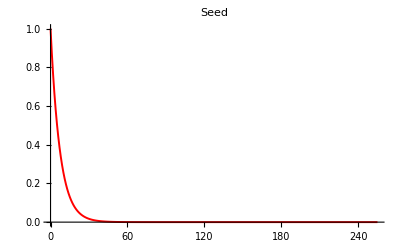
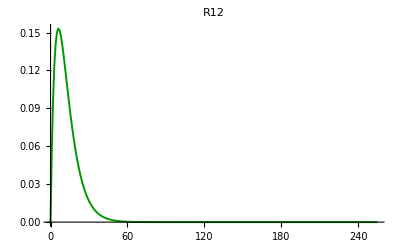
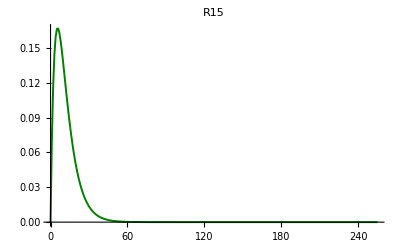
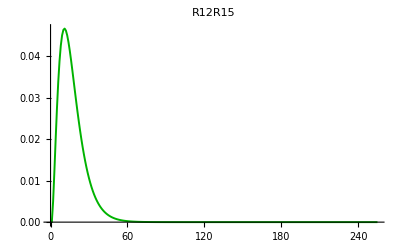
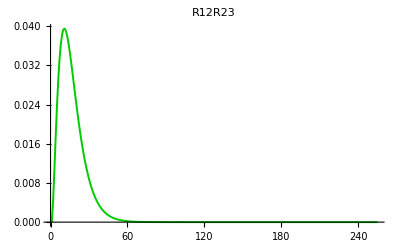
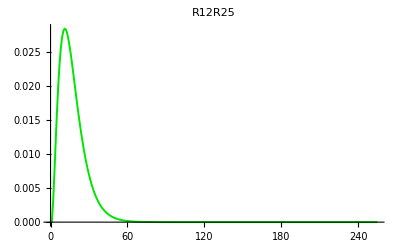
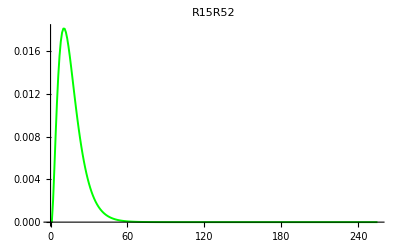
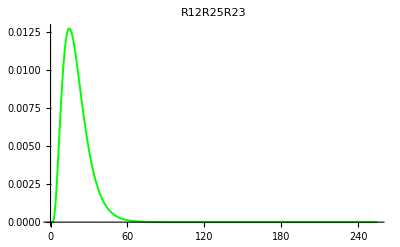

```mathematica
plotsLine
```

First plot

```mathematica
xEndRange=70;
```

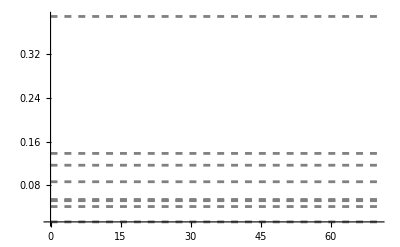

```mathematica
analyticalLines=Plot[{1/77,4/77,9/77,30/77,12/231,32/231,20/231,19/462,25/462},{x,0,xEndRange},
PlotStyle->Directive[Gray,Dashed],
PlotRange->All(*,PlotLegends->{"1/11","2/11","3/11","5/11"},*)
]
```

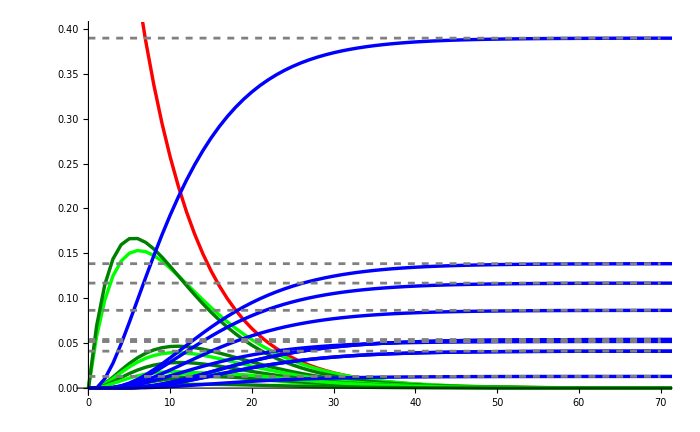

```mathematica
textx=xEndRange+20;
Show[{plotsLine,analyticalLines},
PlotLabel->None,
PlotRange->{{0,xEndRange},{0,4/10}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
(*AxesLabel->{δt,w},*)
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,20},{Automatic,Automatic}},
Background->None]
```

With gamma=0.15

```mathematica
gamma=0.15;

plotsLine=Table[
ListLinePlot[
Times[{gamma,1},#]&/@dataConv[[2;;-1,{1,i}]],
PlotRange->All, 
PlotLabel->dataConv[[1,i]]
],
{i,2,Length[dataConv[[1]]]}];
```

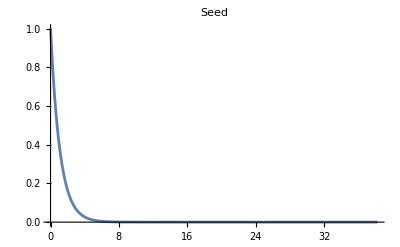
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotsLine
```

```mathematica
size=0.0035;
plotsLine=plotsLine/. Line[x_]:>{Thickness[size],Line[x]};
plotsLine[[1]]=plotsLine[[1]]/. Line[x_]:>{Thickness[size],Red,Line[x]};
plotsLine[[3]]=plotsLine[[3]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[2]]=plotsLine[[2]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[4]]=plotsLine[[4]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[5]]=plotsLine[[5]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[6]]=plotsLine[[6]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[7]]=plotsLine[[7]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[8]]=plotsLine[[8]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[9]]=plotsLine[[9]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[10]]=plotsLine[[10]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[11]]=plotsLine[[11]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[12]]=plotsLine[[12]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[13]]=plotsLine[[13]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[14]]=plotsLine[[14]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[15]]=plotsLine[[15]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[16]]=plotsLine[[16]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[17]]=plotsLine[[17]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[18]]=plotsLine[[18]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[19]]=plotsLine[[19]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[20]]=plotsLine[[20]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
```

```mathematica
xEndRange=70*gamma;
```

```mathematica
analyticalLines=Plot[{1/77,4/77,9/77,30/77,12/231,32/231,20/231,19/462,25/462},{x,0,xEndRange},
PlotStyle->Directive[Gray,Dashed],
PlotRange->All(*,PlotLegends->{"1/11","2/11","3/11","5/11"},*)
]
```

-Graphics-

```mathematica
Replace[{1/77,4/77,9/77,30/77,12/231,32/231,20/231,19/462,25/462},a_:>Text[ToString[Numerator[a]]/ToString[Denominator[a]],{textx,a}],1]
```

{Text[1/77,{30.5,1/77}],Text[4/77,{30.5,4/77}],Text[9/77,{30.5,9/77}],Text[30/77,{30.5,30/77}],Text[4/77,{30.5,4/77}],Text[32/231,{30.5,32/231}],Text[20/231,{30.5,20/231}],Text[19/462,{30.5,19/462}],Text[25/462,{30.5,25/462}]}

```mathematica
textx=xEndRange-1;
Show[{plotsLine,analyticalLines},
PlotLabel->None,
PlotRange->{{0,xEndRange},{0,4/10}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
(*AxesLabel->{δt,w},*)
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,20},{Automatic,Automatic}},
Background->None
(*Epilog->{Text[("1")/("77"),{textx,1/77}],Text[("4")/("77"),{textx,4/77}],Text[("9")/("77"),{textx,9/77}],Text[("30")/("77"),{textx,30/77}],Text[("4")/("77"),{textx,4/77}],Text[("32")/("231"),{textx,32/231}],Text[("20")/("231"),{textx,20/231}],Text[("19")/("462"),{textx,19/462}],Text[("25")/("462"),{textx,25/462}]}*)]
```

-Graphics-

```mathematica
textx=xEndRange-1;
Show[{plotsLine,analyticalLines},
PlotLabel->None,
PlotRange->{{0,xEndRange},{0,0.18}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
(*AxesLabel->{δt,w},*)
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,20},{Automatic,Automatic}},
Background->None,
Epilog->{Text[("1")/("77"),{textx,1/77}],Text[("4")/("77"),{textx,4/77}],Text[("9")/("77"),{textx,9/77}],Text[("30")/("77"),{textx,30/77}],Text[("4")/("77"),{textx,4/77}],Text[("32")/("231"),{textx,32/231}],Text[("20")/("231"),{textx,20/231}],Text[("19")/("462"),{textx,19/462}],Text[("25")/("462"),{textx,25/462}]}]
```

-Graphics-

DLAconvergenceData2026-01-23-14h36

```mathematica
dataConv=Drop[Import["..\\Data\\DLAconvergenceData2026-01-23-14h36.csv","CSV"],0];
```

Points

```mathematica
ClearAll[plots]
```

```mathematica
dataConv[[-1]]
```

{1000,0.000203969,0.000235155,0.000169347,0.000166456,0.000139568,0.000115334,0.0000511223,0.0000877362,0.000109605,0.0000218691,0.138328,0.0518872,0.0539797,0.0539797,0.0410188,0.0410188,0.0129609,0.38941,0.116715,0.0864407,0.0129609}

```mathematica
plots=Table[
ListPlot[
dataConv[[2;;-1,{1,i}]],PlotRange->All, PlotLabel->dataConv[[1,i]]
],
{i,2,Length[dataConv[[1]]]}];
```

```mathematica
plots
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[{plots[[-6]],plots[[-5]]/.Point[x_]:>{PointSize[0.001],Red,Point[x]}}]
```

-Graphics-

Lines

```mathematica
gamma=1;
(*WITH CALLOUT*)
plotsLine=Table[
ListLinePlot[
Callout[Times[{gamma,1},#]&/@dataConv[[2;;-1,{1,i}]],dataConv[[1,i]],Above],
PlotRange->All, 
PlotLabel->dataConv[[1,i]](*,
PlotLegends->dataConv[[1,i]]*)
],
{i,2,Length[dataConv[[1]]]}];
```

```mathematica
size=0.0035;
plotsLine=plotsLine/. Line[x_]:>{Thickness[size],Line[x]};
plotsLine[[1]]=plotsLine[[1]]/. Line[x_]:>{Thickness[size],Red,Line[x]};
plotsLine[[3]]=plotsLine[[3]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[2]]=plotsLine[[2]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[4]]=plotsLine[[4]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[5]]=plotsLine[[5]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[6]]=plotsLine[[6]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[7]]=plotsLine[[7]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[8]]=plotsLine[[8]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[9]]=plotsLine[[9]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[10]]=plotsLine[[10]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[11]]=plotsLine[[11]]/. Line[x_]:>{Thickness[size],Dashed,Blue,Line[x]};
plotsLine[[12]]=plotsLine[[12]]/. Line[x_]:>{Thickness[size],Dashed,Blue,Line[x]};
plotsLine[[13]]=plotsLine[[13]]/. Line[x_]:>{Thickness[size],Cyan,Line[x]};
plotsLine[[14]]=plotsLine[[14]]/. Line[x_]:>{Thickness[size],Dashed,Blue,Line[x]};
plotsLine[[15]]=plotsLine[[15]]/. Line[x_]:>{Thickness[size],Cyan,Line[x]};
plotsLine[[16]]=plotsLine[[16]]/. Line[x_]:>{Thickness[size],Dashed,Blue,Line[x]};
plotsLine[[17]]=plotsLine[[17]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[18]]=plotsLine[[18]]/. Line[x_]:>{Thickness[size],Dashed,Blue,Line[x]};
plotsLine[[19]]=plotsLine[[19]]/. Line[x_]:>{Thickness[size],Dashed,Blue,Line[x]};
plotsLine[[20]]=plotsLine[[20]]/. Line[x_]:>{Thickness[size],Dashed,Blue,Line[x]};
plotsLine[[21]]=plotsLine[[21]]/. Line[x_]:>{Thickness[size],Dashed,Cyan,Line[x]};
```

```mathematica
plotsLine
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
xEndRange=1200;
Show[plotsLine,
AxesOrigin->{xEndRange,0},
PlotLabel->None,
PlotRange->{{500,xEndRange},{0,0.05}}
]
```

-Graphics-

First plot

```mathematica
xEndRange=800;
```

```mathematica
analyticalLines=Plot[{1/77,4/77,9/77,30/77,12/231,32/231,20/231,19/462,25/462},{x,0,xEndRange},
PlotStyle->Directive[Gray,Dashed],
PlotRange->All(*,PlotLegends->{"1/11","2/11","3/11","5/11"},*)
]
```

-Graphics-

```mathematica
textx=xEndRange+20;
Show[{plotsLine,analyticalLines},
PlotLabel->None,
PlotRange->{{0,xEndRange},{0,4/10}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
(*AxesLabel->{δt,w},*)
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,20},{Automatic,Automatic}},
Background->None]
```

-Graphics-

With gamma=0.01

```mathematica
dataConv[[1]]
```

{#i,Seed,R12,R15,R12R15,R12R23,R12R25,R15R52,R12R25R23,R15R52R23,R12R15R54,R15R52R54,R12R15R23R34,R12R15R23R54,R12R25R23R34,R12R25R23R54,R15R52R23R54,R15R54,R12R23R34,R12R25R54,R15R52R23R34}

```mathematica
gamma=0.01;
(*WITH CALLOUT*)
plotsLine=Table[
ListLinePlot[
Callout[Times[{gamma,1},#]&/@dataConv[[2;;-1,{1,i}]],dataConv[[1,i]],Above],
PlotRange->All, 
PlotLabel->dataConv[[1,i]](*,
PlotLegends->dataConv[[1,i]]*)
],
{i,2,Length[dataConv[[1]]]}];
```

```mathematica
plotsLine=Table[
ListLinePlot[
Times[{gamma,1},#]&/@dataConv[[2;;-1,{1,i}]],
PlotRange->All, 
PlotLabel->dataConv[[1,i]](*,
PlotLegends->dataConv[[1,i]]*)
],
{i,2,Length[dataConv[[1]]]}];
```

```mathematica
plotsLine
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
size=0.0035;
plotsLine=plotsLine/. Line[x_]:>{Thickness[size],Line[x]};
plotsLine[[1]]=plotsLine[[1]]/. Line[x_]:>{Thickness[size],Red,Line[x]};
plotsLine[[3]]=plotsLine[[3]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[2]]=plotsLine[[2]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[4]]=plotsLine[[4]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[5]]=plotsLine[[5]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[6]]=plotsLine[[6]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[7]]=plotsLine[[7]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[8]]=plotsLine[[8]]/. Line[x_]:>{Thickness[size],RGBColor[0, 1, 0],Line[x]};
plotsLine[[9]]=plotsLine[[9]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[10]]=plotsLine[[10]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.5, 0],Line[x]};
plotsLine[[11]]=plotsLine[[11]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[12]]=plotsLine[[12]]/. Line[x_]:>{Thickness[size],RGBColor[0, 0.45, 1],Line[x]};
plotsLine[[13]]=plotsLine[[13]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[14]]=plotsLine[[14]]/. Line[x_]:>{Thickness[size],Dashed,Yellow,Line[x]};
plotsLine[[15]]=plotsLine[[15]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[16]]=plotsLine[[16]]/. Line[x_]:>{Thickness[size],Dashed,Yellow,Line[x]};
plotsLine[[17]]=plotsLine[[17]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[18]]=plotsLine[[18]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[19]]=plotsLine[[19]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[20]]=plotsLine[[20]]/. Line[x_]:>{Thickness[size],Blue,Line[x]};
plotsLine[[21]]=plotsLine[[21]]/. Line[x_]:>{Thickness[size],Dashed,Yellow,Line[x]};
```

```mathematica
xEndRange=800*gamma;
```

```mathematica
analyticalLines=Plot[{1/77,4/77,9/77,30/77,12/231,32/231,20/231,19/462,25/462},{x,0,xEndRange*2},
PlotStyle->Directive[Gray,Dashed,Thickness[0.001]],
PlotRange->All(*,PlotLegends->{"1/11","2/11","3/11","5/11"},*)
]
```

-Graphics-

```mathematica
textx=xEndRange-1;
Show[{plotsLine/. Callout[expr_,___]:>expr,analyticalLines},
PlotLabel->None,
PlotRange->{{0,xEndRange},{0,4/10}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
(*AxesLabel->{δt,w},*)
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,20},{Automatic,Automatic}},
Background->None
(*Epilog->{Text[("1")/("77"),{textx,1/77}],Text[("4")/("77"),{textx,4/77}],Text[("9")/("77"),{textx,9/77}],Text[("30")/("77"),{textx,30/77}],Text[("4")/("77"),{textx,4/77}],Text[("32")/("231"),{textx,32/231}],Text[("20")/("231"),{textx,20/231}],Text[("19")/("462"),{textx,19/462}],Text[("25")/("462"),{textx,25/462}]}*)]
```

-Graphics-

```mathematica
xEndRange=8.5;
textx=xEndRange-1;
Show[{plotsLine[[1;;10]],analyticalLines},
PlotLabel->None,
PlotRange->{{0,xEndRange},{0,0.055}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
(*AxesLabel->{δt,w},*)
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,20},{Automatic,Automatic}},
Background->None(*,
Epilog->{Text[("1")/("77"),{textx,1/77}],Text[("4")/("77"),{textx,4/77}],Text[("9")/("77"),{textx,9/77}],Text[("30")/("77"),{textx,30/77}],Text[("4")/("77"),{textx,4/77}],Text[("32")/("231"),{textx,32/231}],Text[("20")/("231"),{textx,20/231}],Text[("19")/("462"),{textx,19/462}],Text[("25")/("462"),{textx,25/462}]}*)]
```

-Graphics-

```mathematica
xEndRange=8.5;
textx=xEndRange-1;
Show[{plotsLine,analyticalLines},
PlotLabel->None,
PlotRange->{{0,xEndRange},{0,0.055}},
PlotRangePadding->{0,0},
PlotRangeClipping->True,
(*AxesLabel->{δt,w},*)
AxesOrigin->{0,0},
ImageSize->{700,400},
ImagePadding->{{Automatic,20},{Automatic,Automatic}},
Background->None(*,
Epilog->{Text[("1")/("77"),{textx,1/77}],Text[("4")/("77"),{textx,4/77}],Text[("9")/("77"),{textx,9/77}],Text[("30")/("77"),{textx,30/77}],Text[("4")/("77"),{textx,4/77}],Text[("32")/("231"),{textx,32/231}],Text[("20")/("231"),{textx,20/231}],Text[("19")/("462"),{textx,19/462}],Text[("25")/("462"),{textx,25/462}]}*)]
```

-Graphics-